```mathematica
data = Import["/Users/bclary/Documents/work/codeprojects/music/test_dft/lvb_buffer_norm2.txt","List"];
```

```mathematica
data = Import["/Users/bclary/Documents/work/codeprojects/music/test_me_freq5.txt","List"];
```

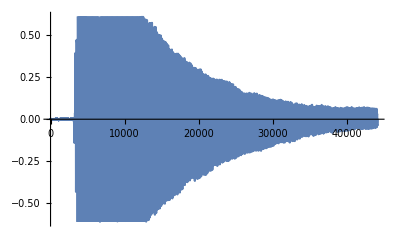

```mathematica
ListLinePlot[data]
```

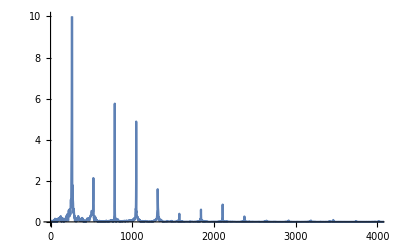

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->{{0,4000},{0,10}}]
```

```mathematica
data=Table[N[Sin[30 2 Pi n/200]+(RandomReal[]-1/2)],{n,200}]
```

{1.27354,0.904711,-0.163937,-0.803314,-1.30906,-0.847976,0.279644,1.08107,0.326877,-0.155028,-0.96769,-0.943293,-0.67302,1.04906,0.701395,0.166619,-0.604837,-0.475331,-1.09703,-0.316163,1.28421,0.882858,0.365602,-0.936152,-1.12147,-0.17146,0.211413,1.34693,1.00211,-0.434111,-1.15087,-0.986621,-0.554745,0.589007,1.41459,0.0981848,-0.488814,-0.882247,-0.627184,-0.431747,1.28218,0.601927,0.624587,-0.186311,-0.984516,-0.642689,0.714665,1.38508,0.31383,0.207351,-0.895438,-0.8838,-0.0455991,0.644939,1.14739,0.908023,-0.528704,-0.859279,-0.410549,0.062308,0.638378,0.876267,0.471656,-0.120042,-0.511351,-0.927834,0.0460944,0.65795,0.811543,-0.497864,-0.839912,-0.662223,-0.0502537,0.276518,0.685164,0.295488,-0.689481,-1.38405,-0.744931,-0.0518469,0.802064,0.976843,0.748134,-0.626584,-1.32325,-0.810343,0.68152,0.509265,0.846255,-0.226334,-1.24003,-1.06517,-0.461094,0.169011,1.3147,0.601562,-0.344105,-1.2669,-0.478695,0.463477,0.333685,0.964234,0.607618,-0.850663,-0.868317,-0.13856,-0.0462883,0.582795,1.16335,0.000702071,-1.00811,-0.990453,-0.295607,0.642521,1.26443,0.388813,-0.254575,-1.3557,-0.352317,0.293879,1.20647,0.789501,0.0191894,-0.855851,-0.915347,-0.322397,0.0467299,1.16225,0.471098,0.0263582,-0.818516,-1.35444,-0.148779,0.97091,0.603979,0.71227,0.0397067,-1.34723,-0.508586,-0.14192,0.320364,0.944375,-0.0431929,-1.03751,-1.04106,-0.444886,0.183544,0.649846,0.740667,0.214435,-0.574374,-1.04486,-0.119611,0.670073,0.540653,0.292746,-0.516741,-0.840419,-1.06821,0.115682,1.19183,0.999603,0.357637,-0.106019,-0.644073,-0.906492,0.374426,1.02418,0.792857,-0.25127,-1.17714,-1.16071,0.130168,0.131142,1.05319,0.70848,-0.144299,-1.37834,-0.406142,0.0527556,1.02022,0.748842,-0.162749,-0.740841,-1.38595,-0.102717,0.740467,1.25818,1.063,0.0903367,-0.840504,-0.859214,-0.151541,0.738084,0.61405,0.217599,0.063957,-0.826664,-0.743398,-0.0171583}

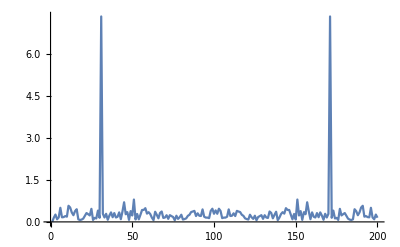

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```